```mathematica
m=Integrate[rho t 2 π(r0+ x Tan[θ]),{x,0,L}]/.Tan[θ]-> (r1-r0)/L//Simplify
```

L π (r0+r1) rho t

```mathematica
cm=(1/m)*Integrate[x(rho t 2 π(r0+ x Tan[θ])),{x,0,L}]/.Tan[θ]-> (r1-r0)/L//Simplify
```

(L (r0+2 r1))/(3 (r0+r1))

```mathematica
Ixx=(Integrate[(r0+x Tan[θ])^2 *(rho t 2 π(r0+ x Tan[θ])),{x,0,L}])/.Tan[θ]-> (r1-r0)/L/.Cot[θ]-> L/(r1-r0)//FullSimplify
```

1/2 L π (r0+r1) (r0^2+r1^2) rho t

```mathematica
Iyy=(Integrate[x^2(rho t 2 π(r0+ x Tan[θ])),{x,0,L}]-m cm^2)/.Tan[θ]-> (r1-r0)/L//FullSimplify
```

(L^3 π (r0^2+4 r0 r1+r1^2) rho t)/(18 (r0+r1))

```mathematica
planformArea = ((cr+ct)/2)*s
```

1/2 (cr+ct) s

```mathematica
l[y_]:=(ct r0-cr r1+cr y-ct y)/(r0-r1)
```

```mathematica
(cr-ct)/(r0-r1) y  - (((cr-ct) r0)/(r0-r1)) + cr//Simplify
```

(ct r0-cr r1+cr y-ct y)/(r0-r1)

```mathematica
Collect[l[y]//Cancel,y]
```

(ct r0-cr r1)/(r0-r1)+((cr-ct) y)/(r0-r1)

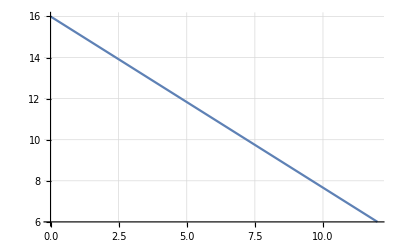

```mathematica
Plot[l[y]/.{cr-> 11, ct-> 6, r0-> 6, r1-> 12},{y,0,12},GridLines->Automatic]
```

```mathematica
dmass[y_]:=rho l[y]t
```

```mathematica
m=Integrate[dmass[y],{y,r0,r1}]/.r1-> r0+s//FullSimplify
```

1/2 (cr+ct) rho s t

```mathematica
cm=(1/m) Integrate[y dmass[y],{y,r0,r1}]/.r1-> r0+s//FullSimplify
```

r0+((cr+2 ct) s)/(3 (cr+ct))

```mathematica
Ixx =  Integrate[y^2 dmass[y],{y,r0,r1}]/.r1-> r0+s//FullSimplify
```

1/12 rho s (6 (cr+ct) r0^2+4 (cr+2 ct) r0 s+(cr+3 ct) s^2) t

```mathematica
Ixx/m//FullSimplify
```

(6 (cr+ct) r0^2+4 (cr+2 ct) r0 s+(cr+3 ct) s^2)/(6 (cr+ct))

```mathematica
Ixx/m//FullSimplify//Apart//Cancel
```

r0^2+(2 (cr+2 ct) r0 s)/(3 (cr+ct))+((cr+3 ct) s^2)/(6 (cr+ct))

```mathematica
m
```

L π (r0+r1) rho t

```mathematica
ddm = rho t l[y]
```

(rho t (ct r0-cr r1+cr y-ct y))/(r0-r1)

```mathematica
dIyyLE = (l[y]^3/3) ddm//Simplify
```

(rho t (ct (r0-y)+cr (-r1+y))^4)/(3 (r0-r1)^4)

```mathematica
dIyycm = dIyyLE - ddm (l[y]/2)^2//Simplify
```

1/(12 (r0-r1)^4)rho t ((-3+4 ct) r0+(3-4 cr) r1+4 (cr-ct) y) (ct (r0-y)+cr (-r1+y))^3

```mathematica
cmy
```

cmy

```mathematica
dIyyCM = dIyycm + ddm(cmy - (y Tan[γ]+l[y]/2))^2//Simplify
```

1/(12 (r0-r1)^4)rho t (((-3+4 ct) r0+(3-4 cr) r1+4 (cr-ct) y) (ct (r0-y)+cr (-r1+y))^3+3 (r0-r1) (ct (r0-y)+cr (-r1+y)) (ct (-2 r0+r1-y)+cr (r0+y)+(r0-r1) (r0-r1+2 y) Tan[γ])^2)

```mathematica
Iyy=Integrate[dIyyCM,{y,r0,r1}]//Simplify
```

1/(480 (r0-r1))rho t (-2 (16 cr^4+cr^3 (-15+16 ct)+cr^2 ct (-15+16 ct)+cr ct^2 (-15+16 ct)+ct^3 (-15+16 ct)) (r0-r1)^2+1/(-ⅈ+Tan[γ])^2 5 Sec[γ]^4 (Cos[2 γ]+ⅈ Sin[2 γ]) (17 cr^3 r0^2-43 cr^2 ct r0^2+5 cr ct^2 r0^2+33 ct^3 r0^2+34 cr r0^4+18 ct r0^4+6 cr^3 r0 r1+14 cr^2 ct r0 r1-34 cr ct^2 r0 r1-10 ct^3 r0 r1-80 cr r0^3 r1-32 ct r0^3 r1+cr^3 r1^2+5 cr^2 ct r1^2+5 cr ct^2 r1^2+ct^3 r1^2+60 cr r0^2 r1^2+12 ct r0^2 r1^2-16 cr r0 r1^3+2 cr r1^4+2 ct r1^4+(ct^3 (33 r0^2-10 r0 r1+r1^2)-2 cr (r0-r1)^2 (17 r0^2-6 r0 r1+r1^2)-2 ct (r0-r1)^2 (9 r0^2+2 r0 r1+r1^2)+cr^3 (17 r0^2+6 r0 r1+r1^2)+cr ct^2 (5 r0^2-34 r0 r1+5 r1^2)+cr^2 ct (-43 r0^2+14 r0 r1+5 r1^2)) Cos[2 γ]+48 r0 (r0-r1) (cr^2 r0-ct^2 r0+cr ct (-r0+r1)) Sin[2 γ]))

```mathematica
Iyy/.r1-> r0+s//Simplify
```

-1/(480 s)rho t (-2 (16 cr^4+cr^3 (-15+16 ct)+cr^2 ct (-15+16 ct)+cr ct^2 (-15+16 ct)+ct^3 (-15+16 ct)) s^2+1/(-ⅈ+Tan[γ])^2 5 Sec[γ]^4 (Cos[2 γ]+ⅈ Sin[2 γ]) (24 cr^3 r0^2-24 cr^2 ct r0^2-24 cr ct^2 r0^2+24 ct^3 r0^2+8 cr^3 r0 s+24 cr^2 ct r0 s-24 cr ct^2 r0 s-8 ct^3 r0 s+cr^3 s^2+5 cr^2 ct s^2+5 cr ct^2 s^2+ct^3 s^2+24 cr r0^2 s^2+24 ct r0^2 s^2-8 cr r0 s^3+8 ct r0 s^3+2 cr s^4+2 ct s^4+(ct^3 (24 r0^2-8 r0 s+s^2)-2 ct s^2 (12 r0^2+4 r0 s+s^2)+cr^3 (24 r0^2+8 r0 s+s^2)+cr^2 ct (-24 r0^2+24 r0 s+5 s^2)-cr (ct^2 (24 r0^2+24 r0 s-5 s^2)+2 s^2 (12 r0^2-4 r0 s+s^2))) Cos[2 γ]-48 r0 s (cr^2 r0-ct^2 r0+cr ct s) Sin[2 γ]))

```mathematica
cmy = ((r1-r0)/2)*Tan[γ]+l[(r1-r0)/2]//Simplify
```

-(ct (-3 r0+r1)+cr (r0+r1)+(r0-r1)^2 Tan[γ])/(2 (r0-r1))

```mathematica
Iyy/.r1-> r0+s//FullSimplify
```

1/(120 s)rho t (60 (cr-ct)^2 (cr+ct) r0^2+20 (cr-ct) (cr^2+4 cr ct+ct^2) r0 s+(8 cr^4+cr^3 (-5+8 ct)+ct^3 (-5+8 ct)+cr^2 ct (5+8 ct)+cr ct^2 (5+8 ct)-60 cr r0^2-60 ct r0^2) s^2+20 (cr-ct) r0 s^3-5 (cr+ct) s^4+5 s (s (12 (cr+ct) r0^2+4 (-cr+ct) r0 s+(cr+ct) s^2) Sec[γ]^2-24 r0 (cr^2 r0-ct^2 r0+cr ct s) Tan[γ]))

```mathematica
Iyy/m/.r1-> r0+s//FullSimplify
```

1/(60 (cr+ct) s^2)(60 (cr-ct)^2 (cr+ct) r0^2+20 (cr-ct) (cr^2+4 cr ct+ct^2) r0 s+(8 cr^4+cr^3 (-5+8 ct)+ct^3 (-5+8 ct)+cr^2 ct (5+8 ct)+cr ct^2 (5+8 ct)-60 cr r0^2-60 ct r0^2) s^2+20 (cr-ct) r0 s^3-5 (cr+ct) s^4+5 s (s (12 (cr+ct) r0^2+4 (-cr+ct) r0 s+(cr+ct) s^2) Sec[γ]^2-24 r0 (cr^2 r0-ct^2 r0+cr ct s) Tan[γ]))

```mathematica
diyy=Integrate[x^2 rho t,{x,y Tan[γ],y Tan[γ] + l[y]}]//Simplify
```

1/3 rho t (-y^3 Tan[γ]^3+((ct r0-cr r1+cr y-ct y)/(r0-r1)+y Tan[γ])^3)

```mathematica
IyyLE=Integrate[diyy,{y,r0,r1}]//FullSimplify
```

1/12 rho t (r0^4 Tan[γ]^3-r1^4 Tan[γ]^3+((r0-r1) (-(cr+r0 Tan[γ])^4+(ct+r1 Tan[γ])^4))/(cr-ct+(r0-r1) Tan[γ]))

```mathematica
IyyLE
```

1/12 rho t (r0^4 Tan[γ]^3-r1^4 Tan[γ]^3+((r0-r1) (-(cr+r0 Tan[γ])^4+(ct+r1 Tan[γ])^4))/(cr-ct+(r0-r1) Tan[γ]))

```mathematica
cmy
```

-(ct (-3 r0+r1)+cr (r0+r1)+(r0-r1)^2 Tan[γ])/(2 (r0-r1))

```mathematica
m
```

1/2 (cr+ct) rho s t

```mathematica
IyyCM = IyyLE - m cmy^2//FullSimplify
```

1/24 rho t (2 r0^4 Tan[γ]^3-2 r1^4 Tan[γ]^3-(3 (cr+ct) s (ct (-3 r0+r1)+cr (r0+r1)+(r0-r1)^2 Tan[γ])^2)/(r0-r1)^2+(2 (r0-r1) (-(cr+r0 Tan[γ])^4+(ct+r1 Tan[γ])^4))/(cr-ct+(r0-r1) Tan[γ]))

```mathematica
iyycmm=IyyCM/m/.r1-> r0+s//FullSimplify
```

-1/(12 (cr+ct) s)(-2 r0^4 Tan[γ]^3+2 (r0+s)^4 Tan[γ]^3+(3 (cr+ct) (2 (cr-ct) r0+(cr+ct) s+s^2 Tan[γ])^2)/s+(2 s (-(cr+r0 Tan[γ])^4+(ct+(r0+s) Tan[γ])^4))/(cr-ct-s Tan[γ]))

```mathematica
iyycmm/.γ-> 0//FullSimplify
```

1/6 (cr^2+ct^2)-(2 (cr-ct) r0+(cr+ct) s)^2/(4 s^2)

```mathematica
iyycmm/.r0-> 0/.γ-> 0//FullSimplify
```

```mathematica
1/12 (-cr^2-6 cr ct-ct^2)/.ct-> cr
```

-(2 cr^2)/3

```mathematica
cm/.r0-> 0
```

(2 L)/3

```mathematica
Iyy/m/.r0-> 0//Simplify
```

L^2/18

```mathematica
Ixx/m/.r0-> 0//Simplify
```

r1^2/2

```mathematica
Iyy/m//Simplify
```

(L^2 (r0^2+4 r0 r1+r1^2))/(18 (r0+r1)^2)

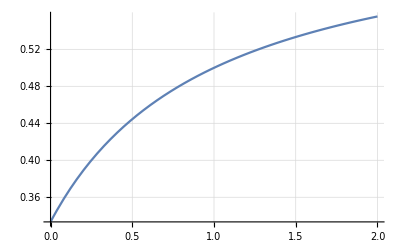

```mathematica
Plot[(1+2 a)/(3 (1+a)),{a,0,2},GridLines->Automatic]
```

```mathematica
tan t = r/x
```